# Practical 3

## Plotting of third order solution family of differential equations

### Q1 : Solve third order differential equation (d^3 y)/dx^3-5(d^2 y)/dx^2+ 8dy/dx - 4y = 0 and plot its any three solutions.

```mathematica
sol = DSolve[y'''[x] - 5 y''[x]+8 y'[x]- 4 y[x]==0, y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^(2 x) C[2]+ⅇ^(2 x) x C[3]}}

```mathematica
sol1 = Evaluate[y[x]/. sol[[1]]/. {C[1]-> 1, C[2] -> 2, C[3] -> 2/3}]
```

ⅇ^x+2 ⅇ^(2 x)+2/3 ⅇ^(2 x) x

```mathematica
sol2 = Evaluate[y[x]/. sol[[1]]/. {C[1]-> 0.5, C[2] -> 2, C[3] -> 3}]
```

0.5 ⅇ^x+2 ⅇ^(2 x)+3 ⅇ^(2 x) x

```mathematica
sol3 = Evaluate[y[x]/. sol[[1]]/. {C[1]-> -1 , C[2] -> -2, C[3] -> 0.5}]
```

-ⅇ^x-2 ⅇ^(2 x)+0.5 ⅇ^(2 x) x

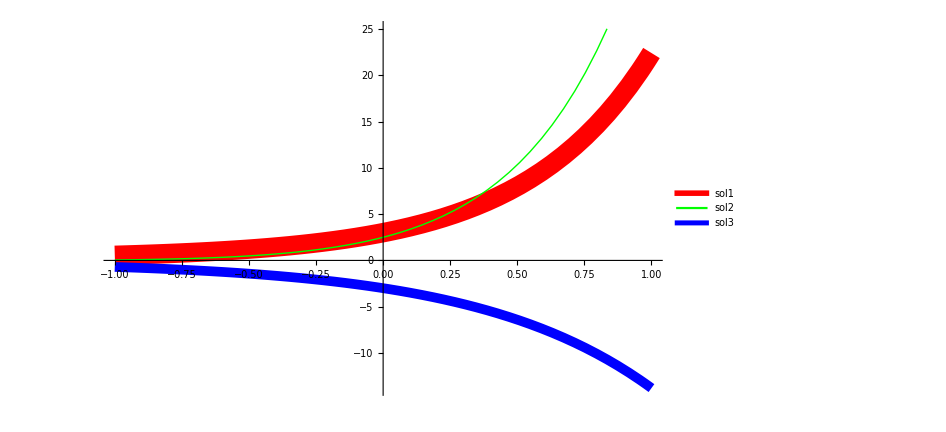

```mathematica
Plot[{sol1,sol2,sol3},{x,-1,1}, ImageSize-> 700, PlotStyle->{{Red, Thickness[0.02]},{Green, Thick},{Blue, Thickness[0.01]}},PlotLegends->Placed[LineLegend["Expressions",LegendLayout -> "Column", LegendFunction->"Frame"],{0.15,0.87}]]
```

### Q2 : Solve third order differential equation (d^3 y)/dx^3+3(d^2 y)/dx^2-25dy/dx + 21y = 0 and plot its any three solutions.

```mathematica
sol = DSolve[y'''[x]+3 y''[x] - 25 y'[x]+ 21 y[x] == 0 ,y[x],x]
```

{{y[x]→ⅇ^(-7 x) C[1]+ⅇ^x C[2]+ⅇ^(3 x) C[3]}}

```mathematica
sol1 = Evaluate[y[x]/. sol[[1]]/. {C[1]-> 1, C[2] -> 2, C[3] -> 3}]
```

ⅇ^(-7 x)+2 ⅇ^x+3 ⅇ^(3 x)

```mathematica
sol2 = Evaluate[y[x]/. sol[[1]]/. {C[1]-> 0.5, C[2] -> 2, C[3] -> -1}]
```

0.5 ⅇ^(-7 x)+2 ⅇ^x-ⅇ^(3 x)

```mathematica
sol3 = Evaluate[y[x]/. sol[[1]]/. {C[1]-> -1 , C[2] -> -2, C[3] -> 0.5}]
```

-ⅇ^(-7 x)-2 ⅇ^x+0.5 ⅇ^(3 x)

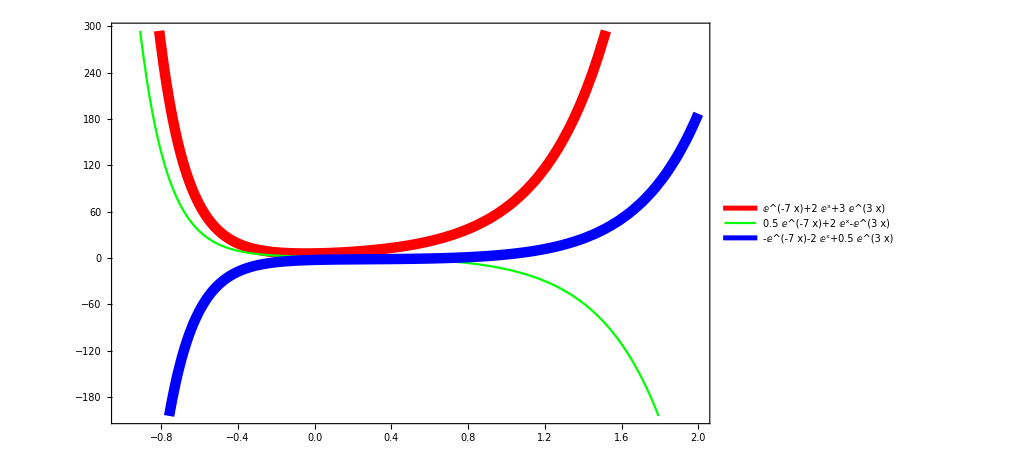

```mathematica
Plot[{sol1,sol2,sol3},{x,-1,2}, ImageSize-> 750, PlotStyle->{{Red, Thickness[0.01]},{Green, Thick},{Blue, Thickness[0.01]}},PlotLegends->{sol1,sol2,sol3},Frame -> True]
```

### Q3 : Solve third order differential equation (d^3 y)/dx^3-4(d^2 y)/dx^2-25dy/dx + 28y = 0 and plot its any three solutions.

```mathematica
pol = DSolve[y'''[x]-4 y''[x] - 25 y'[x]+ 28 y[x] == 0 ,y[x],x]
```

{{y[x]→ⅇ^(-4 x) C[1]+ⅇ^x C[2]+ⅇ^(7 x) C[3]}}

```mathematica
pol1 = Evaluate[y[x]/. pol[[1]]/. {C[1]-> 1, C[2] -> 2, C[3] -> 3}]
```

ⅇ^(-4 x)+2 ⅇ^x+3 ⅇ^(7 x)

```mathematica
pol2= Evaluate[y[x]/. pol[[1]]/. {C[1]-> -1, C[2] -> -2, C[3] -> 1.3}]
```

-ⅇ^(-4 x)-2 ⅇ^x+1.3 ⅇ^(7 x)

```mathematica
pol3 = Evaluate[y[x]/. pol[[1]]/. {C[1]-> 3/2, C[2] -> 0.5, C[3] -> 2.5}]
```

(3 ⅇ^(-4 x))/2+0.5 ⅇ^x+2.5 ⅇ^(7 x)

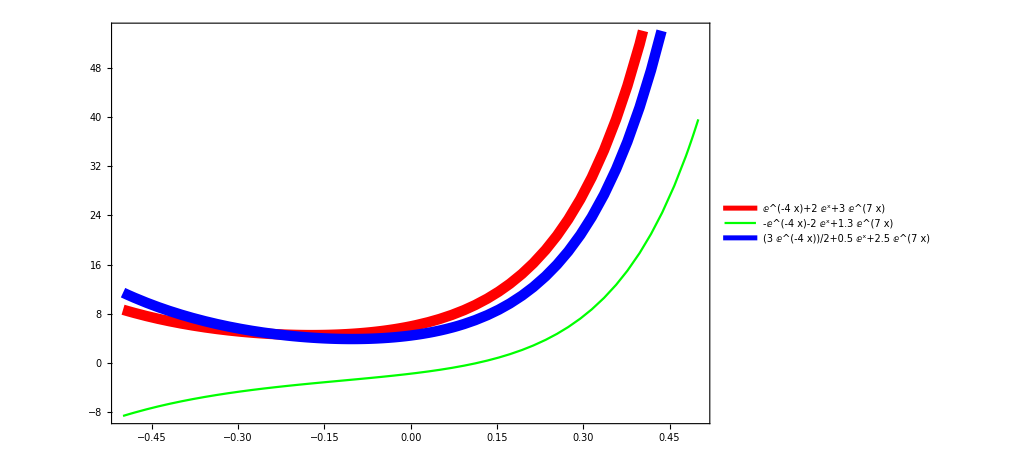

```mathematica
Plot[{pol1,pol2,pol3},{x,-0.5,0.5}, ImageSize-> 750, PlotStyle->{{Red, Thickness[0.01]},{Green, Thick},{Blue, Thickness[0.01]}},PlotLegends->{pol1,pol2,pol3},Frame -> True]
```

### Q4 : Solve third order differential equation (d^3 y)/dx^3-13(d^2 y)/dx^2+19dy/dx + 33y = Cos2x and plot its any three solutions.

{{y[x]→ⅇ^-x C[1]+ⅇ^(3 x) C[2]+ⅇ^(11 x) C[3]+(17 Cos[2 x]+6 Sin[2 x])/1625}}

ⅇ^-x+2 ⅇ^(3 x)+3 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

-ⅇ^-x-2 ⅇ^(3 x)+1.3 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

(3 ⅇ^-x)/2+0.5 ⅇ^(3 x)-2.5 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

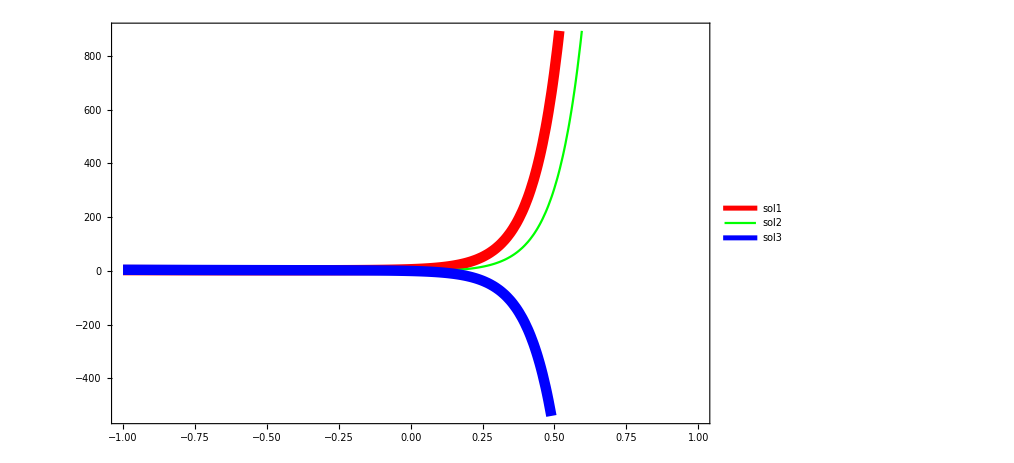

```mathematica
sol = DSolve[y'''[x]-13 y''[x] +19 y'[x]+ 33 y[x] == Cos[2x] ,y[x],x]
sol1 = Evaluate[y[x]/. sol[[1]]/. {C[1]-> 1, C[2] -> 2, C[3] -> 3}]
sol2 = Evaluate[y[x]/. sol[[1]]/. {C[1]-> -1, C[2] -> -2, C[3] -> 1.3}]
sol3 = Evaluate[y[x]/. sol[[1]]/. {C[1]-> 3/2 , C[2] ->0.5, C[3] -> -2.5}]
Plot[{sol1,sol2,sol3},{x,-1,1}, ImageSize-> 750, PlotStyle->{{Red, Thickness[0.01]},{Green, Thick},{Blue, Thickness[0.01]}},PlotLegends->Placed[{"sol1","sol2","sol3"},Below],Frame -> True]
```